```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]]
Off[CloudConnect::verr]
```

/home/edwin/Dropbox/Cinvestav Experiments/Practice/Analysis/Tracker/01062023/Videos

### Parameters

```mathematica
(*Temperature Dataset*)
Tdata=Flatten@Import["temp/LM35Video*.mx"];
T=Mean[Tdata](*K*);
```

```mathematica
(*Parameters*)
diameter=1.23 10^-6(*m*);
kB=1.38064900×10^-23(*J/K*);
r=diameter/2(*m*);
```

```mathematica
(*Parameter Errors*)
σT=StandardDeviation[Tdata](*K*);
σr=3.6 10^-7/2(*m*);
σkB=3.7 10^-7 10^-23(*J/K*);
```

```mathematica
(*Portion to Analyse*)
γ=Floor[n/8.];
```

### Data Analysis

```mathematica
(*Import Data*)
nFile=Length@FileNames["data/analysis*.txt"];
data1=Table[Drop[Import[FileNames["data/analysis*.txt"][[i]],"Data"],2],{i,nFile}];
Lengths1=Table[Length@data1[[i]],{i,nFile}];
nmax=Min[Lengths1];
data=Table[Take[data1[[i]],nmax],{i,nFile}];
Lengths=Table[Length@data[[i]],{i,nFile}];
If[
Chop@StandardDeviation[Lengths]==0,,
Print[Style["Error: ",Red], "Number of frames is not the same for each particle."];Print["Corrupted Files:"];Do[If[Lengths[[i]]≠Max[Lengths],Print@FileNames["data/analysis*.txt"][[i]]],{i,nFile}];Interrupt[]];
```

```mathematica
(*Get Data Information*)
n=Length[data[[1]]];
(*Time*)
t=data[[1,All,1]];
Δt=Drop[Drop[t,1],-(n-γ)];
If[
Chop@StandardDeviation[Differences[t]]==0,
σt=Differences[t][[1]] (*s*),
Print["Error: Δt is not the same per frame."];Interrupt[]];
(*Position*)
x=Table[data[[i,All,2]],{i,nFile}];
y=Table[data[[i,All,3]],{i,nFile}];
```

```mathematica
(*Differences*)
Δy=Table[Table[Table[y[[k,i+j]]-y[[k,i]],{i,n-j}],{j,n-1}],{k,nFile}];
Δx=Table[Table[Table[x[[k,i+j]]-x[[k,i]],{i,n-j}],{j,n-1}],{k,nFile}];
(*Displacements*)
r2=Table[Table[Δx[[k,i]]^2+Δy[[k,i]]^2,{i,n-1}],{k,nFile}];
r2Joined=r2[[1]];
Do[r2Joined=Join[r2Joined,r2[[i+1]],2],{i,nFile-1}];
```

```mathematica
(*Mean Squared Displacement*)
MSD=Table[Mean[r2Joined[[i]]],{i,γ-1}];
(*Standar Deviation*)
σ=Table[StandardDeviation[r2Joined[[i]]]/(√(n-i)),{i,γ-2}];
(*Slope of the MSD*)
MSDData=Drop[Transpose[{Δt,MSD}],-1];
MSDF=LinearModelFit[MSDData,X,X,Weights->1/σ^2];
```

```mathematica
(*Diffusion Coefficient*)
β=D[MSDF["BestFit"],X];
DC=β/2;
(*Viscosity*)
η=(kB T)/(3 π r β);
(*Normalization*)
OrderMagnitude[x_]:=Floor[Log10[Abs[x]]];
OM=OrderMagnitude[Max@MSD];
MaxOM=10^OM;
```

### Error Analysis

```mathematica
(*Slope Error*)
σβ=MSDF["ParameterErrors"][[2]];
(*Diffusion Error*)
σDC=1/2 σβ;
(*Viscosity Error*)
ση=η √((σβ/β)^2+(σkB/kB)^2+(σr/r)^2+(σT/T)^2);
```

```mathematica
(*Fit Error Band Normalized*)
A=MSDF["BestFitParameters"][[1]];
σA=MSDF["ParameterErrors"][[1]];
σFit=√(σA^2+Δt^2 σβ^2+β^2 σt^2);
(*FitError Neglegible*)
Max@σFit/Max@MSD
```

0.0273104

### Fit Statistics

```mathematica
(*Degrees of Freedom*)
ν=MSDF["ANOVATable"][[1,1,4,2]];
(*Reduced χ^2*)
χ2ν=Sum[(MSDF["StandardizedResiduals"]^2)[[i]],{i,Length@MSDF["StandardizedResiduals"]}]/ν;
(*Probability*)
P=SurvivalFunction[ChiSquareDistribution[ν],χ2ν ν];
```

### Theoretical Model

```mathematica
(*Normalized Model*)
MSDT=(kB T Δt)/(3π ηT r)1/MaxOM;
(*MSD Error*)
σMSDT=MSDT √((σηT/ηT)^2+(σkB/kB)^2+(σr/r)^2+(σT/T)^2+(σt/Δt)^2);
(*MSDvsTime*)
MSDTData=Transpose[{Δt,MSDT}];
MSDTDataP=Transpose[{Δt,MSDT+σMSDT}];
MSDTDataM=Transpose[{Δt,MSDT-σMSDT}];
```

```mathematica
(*Data from NIST*)
ηTData={{15.,1.1383},{20.,1.0020},{23.,0.9324},{25.,0.8903},{30.,0.7940},{40,0.6527}};
(*Viscosity*)
ηT=LinearModelFit[ηTData,{1,X,X^2},X][T-273.15] 10^-3;
σηT=0.0015 10^-3 (*Pa s*);
```

```mathematica
(*Diffusion Coefficient DC*)
DCT=(2kB T)/(3π ηT r)(*m^2/s*);
(*Error DC*)
σDCT=DCT √((σkB/kB)^2+(σT/T)^2+(σηT/ηT)^2+(σr/r)^2);
```

#### Validity Limit

```mathematica
(*Limit t>>m/α*)
α=6π ηT r;
V=4/3 π r^3;
ρ=8/100 10^3 (*kg/m^3*);
m=ρ V; (*Mass in kg*)
m/α
```

7.81187×10^-9

### Print Results

Numerical Results

D = 2.23×10^-13 ± 3.35×10^-16 m^2/s

DT = 1.66×10^-12 ± 4.85×10^-13 m^2/s

η = 1.60×10^-3 ± 4.69×10^-4 Pa s

ηT = 8.61×10^-4 ± 1.50×10^-6 Pa s

R^2 = 0.9999

ν = 35.

χ_ν^2 = 1.444

P(χ_ν^2;ν) = 0.04335

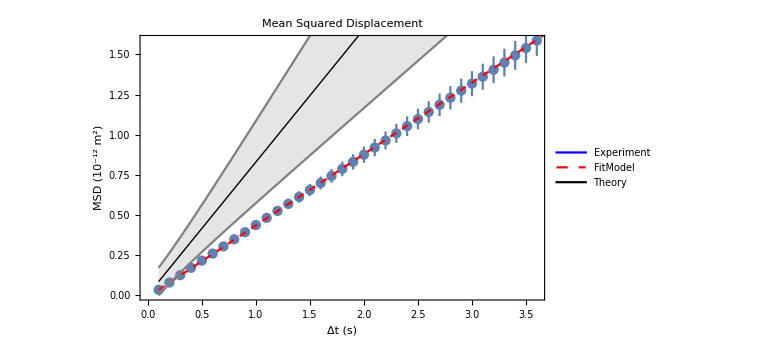

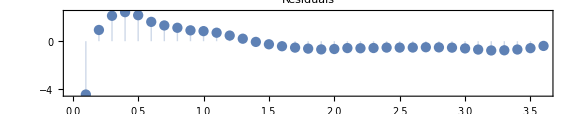

```mathematica
(*Numerical Results*)
Print[]
Print[Style["Numerical Results",Underlined]]
Print["D = ", SetPrecision[ScientificForm@DC,3]," ± ",SetPrecision[ScientificForm@σDC,3]," m^2/s"]
Print["DT = ", SetPrecision[ScientificForm@DCT,3]," ± ",SetPrecision[ScientificForm@σDCT,3]," m^2/s"]
Print["η = ", SetPrecision[ScientificForm@η,3]," ± ",SetPrecision[ScientificForm@ση,3]," Pa s"]
Print["ηT = ", SetPrecision[ScientificForm@ηT,3]," ± ",SetPrecision[ScientificForm@σηT,3]," Pa s"]
Print["R^2 = ", SetPrecision[MSDF["RSquared"],4]]
Print["ν = ", SetPrecision[ν,4]]
Print["χ_ν^2 = ", SetPrecision[χ2ν,4]]
Print["P(χ_ν^2;ν) = ", SetPrecision[P,4]]
Print[]
(*Plots*)
MSDσ=MapAt[ErrorBar,Transpose[{Drop[Transpose[{Δt,MSD/MaxOM}],-1],σ/MaxOM}],{All,2}];
label=StringTemplate["MSD (10^(`OM`) m^2)"][<|"OM"->OM|>];
plot=Show[
ErrorListPlot[MSDσ],
Plot[MSDF["BestFit"]/MaxOM,{X,First[Δt],Last[Δt]},
PlotStyle->{Red,Dashed}],
ListLinePlot[{MSDTData,MSDTDataP,MSDTDataM},
PlotStyle->{{Thick,Black},Gray,Gray},
Filling->{2->{3}}],
FrameLabel->{"Δt (s)",label},
PlotLabel->"Mean Squared Displacement",
Frame->True,
ImageSize->Large];

MSDPlot=Legended[plot,Placed[LineLegend[{Blue,{Dashed,Red},{Thick,Black}},{"Experiment","FitModel","Theory"},LegendFunction->Panel],{{0.05,0.7},{0,0}}]]
ResPlot=ListPlot[Transpose[{Drop[Δt,-1],MSDF["StandardizedResiduals"]}],
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"Δt (s)",""},
PlotLabel->"Residuals"]
```

#### Histograms

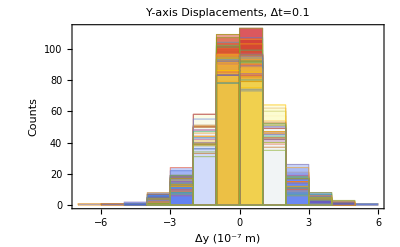

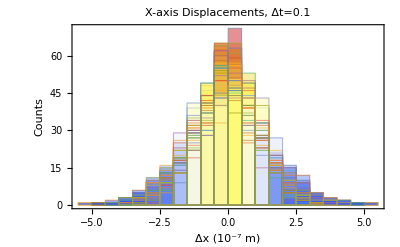

```mathematica
(*Histogram Order of Magnitude*)
OMΔy=OrderMagnitude[Max@Δy[[All,1]]];
MaxOMΔy=10^OMΔy;
(*Histogram Labels*)
labelHistoΔy=StringTemplate["Δy (10^(`OMΔy`) m)"][<|"OMΔy"->OMΔy|>];
labelHistoΔx=StringTemplate["Δx (10^(`OMΔx`) m)"][<|"OMΔx"->OMΔy|>];
(*Histogram Normalization*)
NΔy=Δy[[All,1]]/MaxOMΔy;
NΔx=Δx[[All,1]]/MaxOMΔy;
(*Histograms Plot*)
HistoΔy=Histogram[NΔy,Frame->True,FrameLabel->{labelHistoΔy,"Counts"},PlotLabel->"Y-axis Displacements, Δt=0.1",ColorFunction->"TemperatureMap"]
HistoΔx=Histogram[NΔx,Frame->True,FrameLabel->{labelHistoΔx,"Counts"},PlotLabel->"X-axis Displacements, Δt=0.1",ColorFunction->"TemperatureMap"]
```

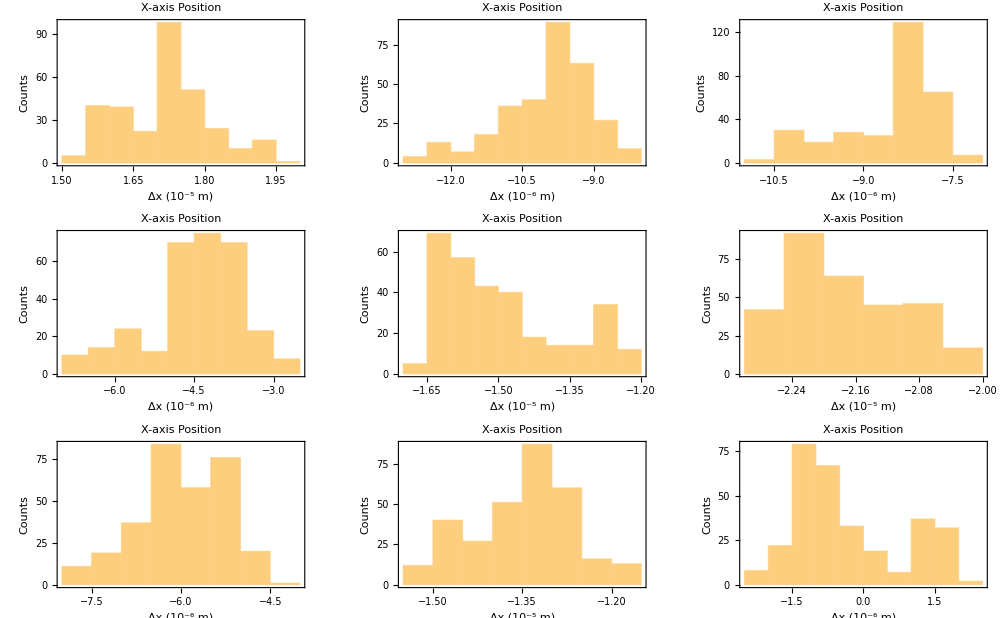

```mathematica
(*Histograms Plot*)
Histox=GraphicsGrid[Table[Table[
(*Histogram Order of Magnitude*)
OMx=OrderMagnitude[Max@x[[(i-1)*3+j]]];
MaxOMx=10^OMx;
(*Histogram Labels*)
labelHistox=StringTemplate["Δx (10^(`OMx`) m)"][<|"OMx"->OMx|>];
(*Histogram Normalization*)
Nx=x[[(i-1)*3+j]]/MaxOMx;
Histogram[Nx,Frame->True,FrameLabel->{labelHistox,"Counts"},PlotLabel->"X-axis Position"],{i,3}],{j,3}],
ImageSize->1000]
```

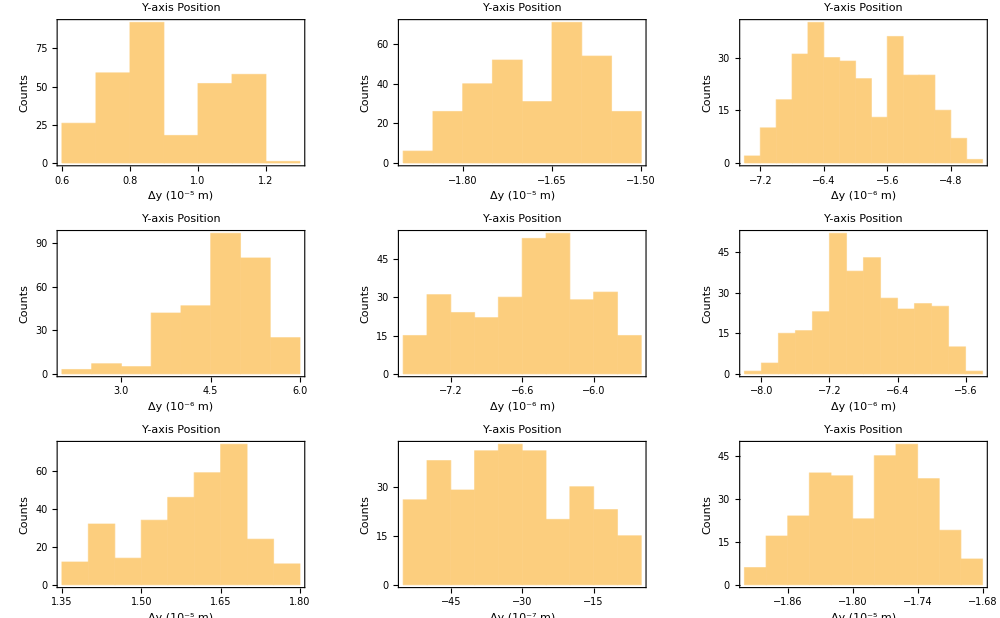

```mathematica
(*Histograms Plot*)
Histoy=GraphicsGrid[Table[Table[
(*Histogram Order of Magnitude*)
OMy=OrderMagnitude[Max@y[[(i-1)*3+j]]];
MaxOMy=10^OMy;
(*Histogram Labels*)
labelHistoy=StringTemplate["Δy (10^(`OMy`) m)"][<|"OMy"->OMy|>];
(*Histogram Normalization*)
Ny=y[[(i-1)*3+j]]/MaxOMy;
Histogram[Ny,Frame->True,FrameLabel->{labelHistoy,"Counts"},PlotLabel->"Y-axis Position"],{i,3}],{j,3}],
ImageSize->1000]
```

```mathematica
(*Export Numerical Results & Plot*)
Export["./results/MSDPlot.pdf",MSDPlot];
Export["./results/Residuals.pdf",ResPlot];
Export["./results/Histody.pdf",HistoΔy];
Export["./results/Histodx.pdf",HistoΔx];
Export["./results/Histox.pdf",Histox];
Export["./results/Histoy.pdf",Histoy];
Export["./results/DC.dat",SetPrecision[DC,3]];
Export["./results/errDC.dat",SetPrecision[σDC,3]];
Export["./results/DCT.dat",SetPrecision[DCT,3]];
Export["./results/errDCT.dat",SetPrecision[σDCT,3]];
Export["./results/Eta.dat", SetPrecision[η,3]];
Export["./results/errEta.dat",SetPrecision[ση,3]];
Export["./results/EtaT.dat",SetPrecision[ηT,3]];
Export["./results/errEtaT.dat",SetPrecision[σηT,3]];Export["./results/R2.dat",SetPrecision[MSDF["RSquared"],4]];Export["./results/DoF.dat",SetPrecision[ν,4]];Export["./results/Chi2.dat",SetPrecision[χ2ν,4]];Export["./results/P.dat",SetPrecision[P,4]];
```